## Assignment 4

5.2.4

(4)(a)  Approximants found from recursion relations can also be used to solve certain nonlinear equations.  For example, consider the equation λ x^3-x + 1=0, where λ<<1. A dominant balance exists between x and 1: if we assume that λ x^3<<1 and drop this term, the solution is x=1. Then λ x^3=λ<<1, which is consistent with our assumption. Set up a recursion relation of the form x_n= 1 + λ (x_(n-1))^3, and solve for x_3, given x_0=1. (No need to Taylor-expand the solution.) Plot the result for 0<λ<1.

(b) The  cubic polynomial in part (a) has three roots, but we only found one approximate solution in part (a).  Evidently there are two other solutions.  Find another dominant balance between two terms in the equation that yields approximations to these solutions, set up a recursion relation, and solve it up to at least x_3.  (Again, no Taylor expansion is necessary.)

(c) Plot the asymptotic expressions found in parts (a) and (b) together on the same graph as a function of λ  for 0<λ<1. Superimpose  these results  on the exact solutions of the cubic equation vs. λ.

### Solution

#### a)

```mathematica
Clear["Global`*"]
```

```mathematica
Clear[x]
```

```mathematica
x[n_] := x[n] = 1 + λ x[n-1]^3;
```

```mathematica
x[0] = 1;
```

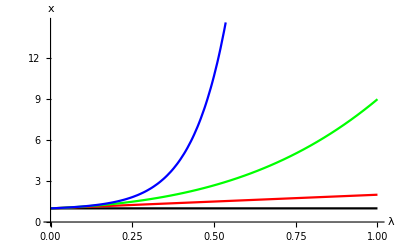

```mathematica
plta=Plot[Evaluate[{x[0],x[1],x[2],x[3]}],{λ,0,1},PlotStyle->{Black,Red,Green,Blue},AxesLabel->{"λ","x"}]
```

#### b)

```mathematica
x2[n_] := Sqrt[1/λ -1/(λ x2[n-1])];
x3[n_] := -Sqrt[1/λ -1/(λ x3[n-1])];
```

```mathematica
x2[0] = Sqrt[1/λ];
x3[0] = -Sqrt[1/λ];
```

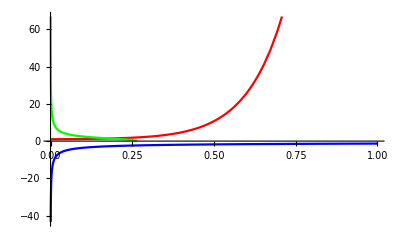

```mathematica
pltb=Plot[Evaluate[{x[3],x2[3],x3[3]}],{λ,0,1},PlotStyle->{Red,Green,Blue}]
```

#### (c)

```mathematica
Solve[λ x^3 - x + 1 ==0,x]
```

{{x→(2/3)^(1/3)/((-9 λ^2+√3 √(-4 λ^3+27 λ^4))^(1/3))+((-9 λ^2+√3 √(-4 λ^3+27 λ^4))^(1/3))/(2^(1/3) 3^(2/3) λ)},{x→-(1+ⅈ √3)/(2^(2/3) 3^(1/3) (-9 λ^2+√3 √(-4 λ^3+27 λ^4))^(1/3))-((1-ⅈ √3) (-9 λ^2+√3 √(-4 λ^3+27 λ^4))^(1/3))/(2 2^(1/3) 3^(2/3) λ)},{x→-(1-ⅈ √3)/(2^(2/3) 3^(1/3) (-9 λ^2+√3 √(-4 λ^3+27 λ^4))^(1/3))-((1+ⅈ √3) (-9 λ^2+√3 √(-4 λ^3+27 λ^4))^(1/3))/(2 2^(1/3) 3^(2/3) λ)}}

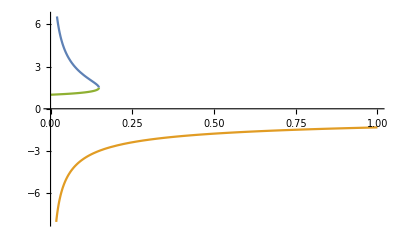

```mathematica
pltexact=Plot[Evaluate[x/.%],{λ,0,1}]
```

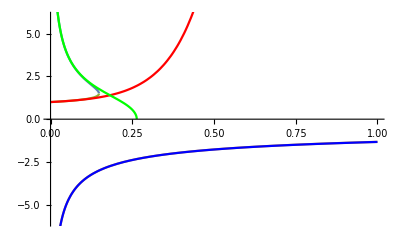

```mathematica
Show[pltexact,pltb,PlotRange->{-6,6}]
```

5.2.6(a)

(6) A simple pendulum with varying length l(t) satisfies the following differential equation:

ⅆ/ⅆt[l^2(t) θ̇(t)]==-g l(t) θ(t) ,

where g=9.8 m/s^2 and θ<<1 is assumed.

(a) Use WKB analysis to determine how θ(t) varies in time, assuming that l(t) varies slowly compared to the frequency, √(g/l(t)). Plot θ(t) assuming that θ(0)=10 °, θ̇(0)=0, and l(t) = 11 - t, for 0<t<10 . Compare with the exact motion, found using NDSolve.

### Solution

#### (a)

Write θ(t) = ⅇ^(S(t)). Then the differential equation implies that
l^2(t) [λ S''+(S')^2] +λ S' ⅆ/ⅆt l^2(t)=-g l(t) .,
where I have placed an ordering parameter λ in front of the small terms. This can be solved order by order. To lowest order, we have
l^2(t)(S')^2 =-g l(t), so  S_o'(t) = ±ⅈ √(g/l(t)). The square root is the usual expression for the frequency ω_o(t) of a pendulum, but now time-varying as the length changes, so we can write
			S_o(t) =±ⅈ∫ⅆt ω_o(t) .

  To next order, we substitute S_o(t) in the small terms to obtain
l^2(t) [λ S_o''+(S_1')^2] +λ S_o' ⅆ/ⅆt l^2(t)=-g l(t). Using the known form for S_o this becomes
l^2(t) [±ⅈ λ ⅆ/ⅆt √(g/l(t))+(S_1')^2] ±ⅈ λ √(g/l(t))ⅆ/ⅆt l^2(t)=-g l(t). Thus,
S_1'=±ⅈ √(g/(l(t))∓ⅈ λ ⅆ/ⅆt √(g/l(t))∓ⅈ λ √(g/l(t))1/l^2 ⅆ/ⅆt l^2(t)).Expand the bracket to first order in λ to obtain
S_1'=±ⅈ ω_o(t)-λ/2 1/ω_o ⅆ/ⅆt ω_o-λ/2 1/l^2 ⅆ/ⅆt l^2(t).  
We can integrate this to obtain
S_1(t) =±ⅈ∫ⅆt ω_o(t) -λ/2 ln ω_o(t)-λ/2 ln l^2(t). 
Thus, the two possible solutions to the problem are
θ(t) = ⅇ^(±ⅈ∫ⅆt ω_o(t))/(l(t)√(ω_o(t))). 
These two independenct solutions can be superimposed to arrive at the general solution to the problem:
θ(t) = (A cos [∫ⅆt ω_o(t)+ϕ])/(l(t)√(ω_o(t))), where A and ϕare undetermined constants in the solution.

```mathematica
Clear["Global`*"]
```

```mathematica
l[t_] = 11-t;g=9.8;
```

```mathematica
ω0[t_] = Sqrt[g/l[t]];
```

```mathematica
ϕ[t_] = Integrate[ω0[t1],{t1,0,t}];
```

```mathematica
θWKB[t_] = 10 Sqrt[l[0]^2 ω0[0]]Cos[ϕ[t]]/Sqrt[l[t]^2 ω0[t]]
```

ConditionalExpression[(60.4011 Cos[3.1305 (2 √11-2/(√(1/(11-t))))])/(√(1/(1/(11-t))^(3/2))),(Re[t]<11&&Re[t]>0&&(11 Re[1/t]>1||1/t∉Reals))||((Re[t]<0||t∉Reals)&&(11 Re[1/t]≥1||Re[1/t]≤0||1/t∉Reals))]

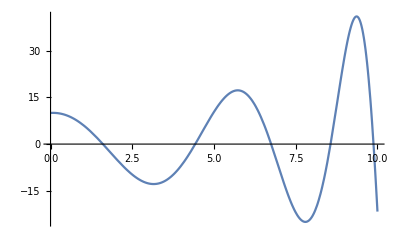

```mathematica
p1=Plot[θWKB[t],{t,0,10}]
```

```mathematica
NDSolve[{D[l[t]^2 θ'[t],t] == -g l[t]  θ[t],θ[0]==10,θ'[0]==0},θ[t],{t,0,10}]
```

{{θ[t]→InterpolatingFunction[{{0., 10.}}, <>][t]}}

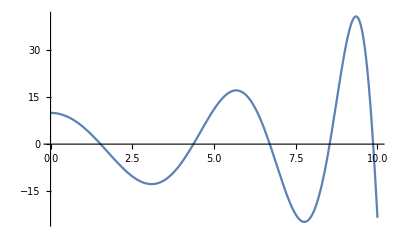

```mathematica
Plot[θ[t]/.%[[1]],{t,0,10}]
```

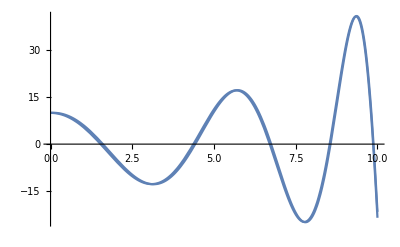

```mathematica
Show[%,p1]
```

5.2.14

(14) In shortwave radio communication, the diffuse plasma in the ionosphere can be used as a mirror to bounce radio waves to receivers beyond the horizon. For  radio waves of frequency ω, the index of refraction is a function of altitude z, and is approximately n(z,ω)=√(1-ω_p^2(z)/ω^2), where ω_p=√(e^2 N(z)/ϵ_o m) is the electron plasma frequency, e and m are the electron charge and mass respectively, and N(z) is the electron density in m^-3. At ground level z=0 the electron density is negligible, but at altitudes on the order of 50-100 km it grows to some maximum value due to the ionizing effect of UV  radiation, and then decays again at still higher altitudes as the atmospheric density falls off.

(a) Show that electromagnetic waves travel through this plasma with the dispersion relation

ω^2=c^2 k^2+ω_p^2(z).

(b)  Show that waves shone directly upward, with k=k ẑ, will reflect back provided that ω<ω_(p max), where ω_(p max) is the maximum plasma frequency. (Hint: Find the turning point for the rays.)

(c) More generally, show that for ω>ω_(p max), there is a maximum angle θ_max with respect to the horizontal at which one can direct the waves, and still have them bounce back. Find an expression for the angle θ_max(ω). (Answer: sin^2 θ_max=(ω_(p max)/ω)^2).

(d) Take the following simple model for the electron density in the ionosphere:

N(z)={0,                                                                            z<H,
5× 10^14 m^-3 (z/H-1)^2 ⅇ^(-10(z/H-1)), z≥ H,

with H=70 km.
Using this model and the results of part (c), trace several ray trajectories for values of θ in the range  0<θ≤  θ_max to show that communication with a receiver closer than a certain distance d(ω)  to the transmitter (but beyond the horizon) is impossible when ω>ω_(p max). Find d(ω) graphically for
  (i) ω=2 π c/10 (10 meter wavelength) and (ii)  ω=2 π c/5.

### Solution

#### (a)

ω = c k/n(z,ω)=c k/√(1-ω_p^2(z)/ω^2). Squaring both sides and doing some algebra yields ω^2=c^2 k^2 + ω_p^2(z).

#### (b)

ⅆz/ⅆt = v_g(k,z)=c^2 k/ω for k=k_z ẑ. However, k=1/c √(ω^2-ω_p^2(z)). Therefore, k→0 wherever ω=ω_p(z) , and so v_g(k,z)=0 at these points (the turning points). Note that ⅆk/ⅆt = -∂ω(z,k)/∂z<0 and so at the turning point where k=0, the negative rate of change of k implies that k becomes negative where is was formerly positive, which implies the wavepacket turns and head back to smaller z.

#### (c)

c) More generally, ⅆz/ⅆt = v_(g z)(k,z)=c^2 k_z/ω, where k_z=1/c √(ω^2-ω_p^2(z)-c^2 k_x^2). We need this to equal zero for a turning point to exist. Therefore, we require 1/c(ω^2-ω_pmax^2-c^2 k_x^2)≤ 0, with equality for the case of minimum θ. Since k_x=k_o cos θ, we have
ω^2-ω_pmax^2=c^2 k_o^2 cos^2 θ_min . But ω^2=c^2 k_o^2, so ω^2-ω_pmax^2=ω^2 cos^2 θ_minwhich implies
sin^2 θ_min=(ω_(p max)/ω)^2.

#### (d)

```mathematica
Clear["Global`*"]
```

```mathematica
H = 70 10^3;
NN[z_] := 0./; z≤ H;
```

```mathematica
NN[z_] :=  5  10^14  (z/H-1)^2 Exp[-10(z/H-1)]/; z>H
```

```mathematica
q = 1.6022 10^-19;
m=9.1095 10^-31;
ϵ0=8.854 10^-12;
c = 2.9979 10^8;
```

```mathematica
ωp[z_] = Sqrt[q^2/(m ϵ0) NN[z]]
```

56.4157 √NN[z]

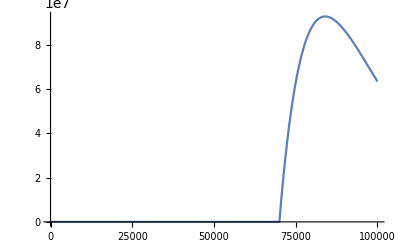

```mathematica
Plot[ωp[z],{z,0,100 10^3}]
```

```mathematica
ωpmax = -FindMinimum[-ωp[z],{z,80 10^4,81 10^4}][[1]]
```

9.28154×10^7

```mathematica
ω[z_,kx_,kz_] = Sqrt[c^2 (kx^2 + kz^2) + ωp[z]^2]
```

√(8.9874×10^16 (kx^2+kz^2)+3182.73 NN[z])

```mathematica
vx[z_,kx_,kz_] = D[ω[z,kx,kz],kx]
```

(8.9874×10^16 kx)/(√(8.9874×10^16 (kx^2+kz^2)+3182.73 NN[z]))

```mathematica
vz[z_,kx_,kz_] = D[ω[z,kx,kz],kz]
```

(8.9874×10^16 kz)/(√(8.9874×10^16 (kx^2+kz^2)+3182.73 NN[z]))

```mathematica
kzp[z_,kx_,kz_] =- D[ω[z,kx,kz],z]
```

-(1591.36 NN'[z])/(√(8.9874×10^16 (kx^2+kz^2)+3182.73 NN[z]))

```mathematica
sol[ω0_,Δθ_] :=(
k0 = ω0/c;
Subscript[θ, min]=ArcSin[ωpmax/ω0]-Δθ;
kx = k0 Cos[Subscript[θ, min]];
kz0 = k0 Sin[Subscript[θ, min]];
{x[t],z[t]}/. NDSolve[{x'[t]== vx[z[t],kx,kz[t]],
z'[t]== vz[z[t],kx,kz[t]],
kz'[t] == kzp[z[t],kx,kz[t]],
z[0]==0,x[0]==0,kz[0]==kz0},{x,z,kz},{t,0, 1000 10^3/c},AccuracyGoal->11,PrecisionGoal->11])
```

```mathematica
Table[ParametricPlot[Evaluate[sol[2 Pi c/10.,Δθ]],{t,0,.0033},PlotRange->{0,100 10^3}],{Δθ,-.0001,.2,.02}];
```

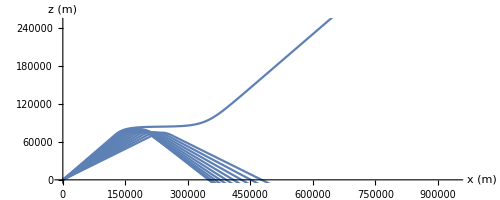

```mathematica
Show[%,AxesLabel->{"x (m)","z (m)"},PlotRange->{All,{0,250000}}]
```

From the graph of ray trajectories, minimum distance is roughly 350 km for the 10 m band

```mathematica
Table[ParametricPlot[Evaluate[sol[2 Pi c/5.,Δθ]],{t,0,.0033},PlotRange->{0,100 10^3}],{Δθ,-.001,.1,.01}];
```

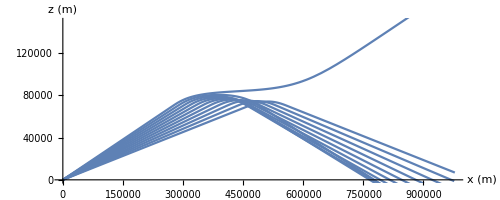

```mathematica
Show[%,AxesLabel->{"x (m)","z (m)"},PlotRange->{All,{0,150000}}]
```

From the graph of ray trajectories, minimum distance is roughly 770 km for the 5 meter band

5.2.16

(16)(a) At a planar interface between two media with refractive indices n_1 and n_2, n_1>n_2, show using Snell's law  that a ray in medium 1 propagating toward the interface  will be completely reflected provided that the angle ψ between the interface and the ray satisfies  ψ<ψ_c= arccos(n_2/n_1). (Hint: Show that no real solution for the refracted-wave angle exists if this inequality is satisfied.)

(b) In an optical fiber, the index of refraction n=n(r) is a decreasing function of cylindrical radius r. In typical fibers the index is of the form n(r)=n_1 (r<a); n=n_2 (r>a), with a=4  μm, n_1=1.451, and n_2=1.444.  The critical angle is then ψ_c=5.63 °.  The point of an optical fiber is that it guides the rays, even if the fiber bends.  Initially, a ray propagates along the axis of the fiber. Then, the fiber is bent into a circle of radius R>>a. Given that n_1 is nearly the same as n_2 so that ψ_c<<1,  show that the ray will be trapped in the fiber provided that R>2a/ ψ_c^2=830 μm (ψ_c measured in radians).

### Solution

#### (a)

Snell’s law:  sin(θ)/c(x)=constant where θ is the angle of incidence. This implies n(x) sin(θ)=constant. The angle ψ=π/2-θ. For two media, n_1 sinθ_1=n_2 sinθ_2 which implies sinθ_2=n_1/n_2 sinθ_1=n_1/n_2 cosψ. This equation has a real solution for θ_2 only if n_1/n_2 cosψ≤ 1, implying  ψ<arccos(n_2/n_1)≡ψ_c. QED.

#### (b)

See the figure below, showig a ray travelling horizontally down the center of a bent optical fibre.
The triangle ABC has angle ψ defined by the relation
cosψ=(R+a)/(R+2a).
SInce R>>a, this can be approximated as cosψ=1-a/R. This implies ψ<<1, so cosψ≈1-ψ^2/2. Therefore, ψ^2/2 = a/R. For total internal reflection, ψ<ψ_c, so a/R<ψ_c^2/2, which implies R>2a/ψ_c^2. QED.